## Private 私有函数

## Public 公有函数

### TIMING 性能测试

返回循环 n 遍所花费的时间和结果

```mathematica
ClearAll[TIMING];

Attributes[TIMING]={HoldAll};

TIMING[code_,n_Integer:1]:=Module[{},
ClearSystemCache[];
(Do[code,n-1];code)//AbsoluteTiming
]

Limit[(x^2+1)/(2 x^2-1),x->∞]//TIMING
```

{0.0012571,1/2}

### ExpressionPivot 表达式主元

返回首个匹配到的非数值符号

```mathematica
ClearAll[ExpressionPivot];

Attributes[ExpressionPivot]={Listable};

ExpressionPivot[expr_]:=FirstCase[expr,_Symbol?(Not@*NumericQ),Symbol,{-1}];

ExpressionPivot[{1,x,a/(a+b),E^x}]//TIMING
```

{0.0000476,{Symbol,x,a,x}}

### CoefficientSeparation 系数分割

返回匹配到的系数和余下部分

```mathematica
ClearAll[CoefficientSeparation];

Attributes[CoefficientSeparation]={Listable};

CoefficientSeparation[expr_,x_Symbol]/;FreeQ[expr,x]:={expr,1};
CoefficientSeparation[expr_,x_Symbol]:=Replace[expr,Longest[c_.]r_/;FreeQ[c,x]->{c,r}];

CoefficientSeparation[{0,(a+b)/2,2/(a+b),(a+b)/(2x),x,-x,2a Sin[x]+4a x,2a Sin[x]+4a x//Simplify},x]//TIMING
```

{0.0014511,{{0,1},{(a+b)/2,1},{2/(a+b),1},{(a+b)/2,1/x},{1,x},{-1,x},{1,4 a x+2 a Sin[x]},{2 a,2 x+Sin[x]}}}

### FirstCoefficient 首系数

返回最高次项的系数

```mathematica
ClearAll[FirstCoefficient];

Attributes[FirstCoefficient]={Listable};

FirstCoefficient[poly_,x_Symbol]:=Coefficient[poly,x,Exponent[poly,x]];

FirstCoefficient[{1,3 x^3-x^2+1,-1/4 x^2+1},x]//TIMING
```

{0.0000646,{1,3,-1/4}}

### PolynomialRoots 多项式根集

返回多项式的根集，速度是 SolveValues 的 10 倍
ToRadicals：是否尝试将结果转换成根式

```mathematica
ClearAll[PolynomialRoots];

Attributes[PolynomialRoots]={Listable};

PolynomialRoots[a_,x_Symbol,OptionsPattern[]]/;FreeQ[a,x]:={};
PolynomialRoots[a_.x_+b_.,x_Symbol,OptionsPattern[]]/;FreeQ[{a,b},x]:={-b/a};
PolynomialRoots[poly_,x_Symbol,OptionsPattern[]]/;PolynomialQ[poly,x]:=List@@(Roots[poly==0,x,Cubics->False,Quartics->False]/.Equal->(#2&));

SolveValues[#==0,x,Cubics->False,Quartics->False]&/@{1,2x-1,3 x^2-4,x^3-x+1,2 x^4-x+1}//Column//TIMING
PolynomialRoots[{1,2x-1,3 x^2-4,x^3-x+1,2 x^4-x+1},x]//Column//TIMING
```

{0.0023367,{}
{1/2}
{-2/(√3),2/(√3)}
{Root-1.32Root[1-#1+#1^3&,1]-1.324717957244746,Root0.662-0.562 ⅈRoot[1-#1+#1^3&,2]0.662358978622373,Root0.662+0.562 ⅈRoot[1-#1+#1^3&,3]0.662358978622373}
{Root-0.607-0.758 ⅈRoot[1-#1+2 #1^4&,1]-0.606835562799765,Root-0.607+0.758 ⅈRoot[1-#1+2 #1^4&,2]-0.606835562799765,Root0.607-0.403 ⅈRoot[1-#1+2 #1^4&,3]0.606835562799765,Root0.607+0.403 ⅈRoot[1-#1+2 #1^4&,4]0.606835562799765}}

{0.0004006,{}
{1/2}
{2/(√3),-2/(√3)}
{Root-1.32Root[1-#1+#1^3&,1]-1.324717957244746,Root0.662-0.562 ⅈRoot[1-#1+#1^3&,2]0.662358978622373,Root0.662+0.562 ⅈRoot[1-#1+#1^3&,3]0.662358978622373}
{Root-0.607-0.758 ⅈRoot[1-#1+2 #1^4&,1]-0.606835562799765,Root-0.607+0.758 ⅈRoot[1-#1+2 #1^4&,2]-0.606835562799765,Root0.607-0.403 ⅈRoot[1-#1+2 #1^4&,3]0.606835562799765,Root0.607+0.403 ⅈRoot[1-#1+2 #1^4&,4]0.606835562799765}}

### PolynomialRootApproximant 多项式根近似

返回多项式的根近似

```mathematica
Clear[PolynomialRootApproximant];

Attributes@PolynomialRootApproximant={Listable};

PolynomialRootApproximant[poly_,x_Symbol]/;PolynomialQ[poly,x]:=FromDigits[RootApproximant/@Reverse@CoefficientList[poly,x],x];

PolynomialRootApproximant[{
12.4839411880551079719990460602151902980707014541089842238980666293350073603842403768400343526743627915530741297725467`94.85237999515779 ,

0.0004451183409375643161809992946796098532659056946184070129760214843561697710836980353795023409035727841522219923812`94.58000822841214+0.0313471893268560893839089749092074553486347633759919308901113309235823869905837499332870757330334211854150054127592`94.65250687328087 x+0.3365872782516560883377401360337685754578375977007642403548030231167455184808257798028720862212793023106416430504819`94.65773124633928 x^2+1.`94.66049314400742 x^3,

0.0659483235720349337722247525188501528217737911194147688016923516305769591286599463361129043540128113481383205426679`95.15774671459718+1.`95.20456715049112 x-0.158443195262402458452935338170328897483451274014428058101509663780586719858557240199135153126834`82.72581141179751+0``82.43377197117319 x
},x]//TIMING
```

{0.0282481,{Root12.5Root[-6075-405 #1^2-153 #1^4+#1^6&,2]12.483941188055107,x^2 (x+Root0.337Root[-7+9 #1+30 #1^2+15 #1^3&,1]0.3365872782516561)+x Root0.0313Root[-1+36 #1-135 #1^2+135 #1^3&,1]0.03134718932685609+Root4.45 × 10^-4Root[-1+2214 #1+72900 #1^2+729000 #1^3&,1]0.0004451183409375643,x+Root-0.0925Root[8+108 #1+270 #1^2+405 #1^3&,1]-0.09249487169036752}}

### IBP 分部积分法

返回分部后的结果
Assumptions：假设，辅助化简

```mathematica
ClearAll[IBP];

Options[IBP]={Assumptions->$Assumptions};

IBP[u_,v_,x_Symbol,OptionsPattern[]]:=Module[{coef,rem},
{coef,rem}=CoefficientSeparation[v D[u,x],x];
u v-coef remx
];
IBP[f_,x_Symbol,OptionsPattern[]]:=IBP[f,x,x];

IBP[u_,v_,{x_Symbol,a_,b_},OptionsPattern[]]:=Module[{assum=OptionValue@Assumptions,c,r},
{c,r}=CoefficientSeparation[v D[u,x],x];
Limit[u v,x->b,Assumptions->assum]-Limit[u v,x->a,Assumptions->assum]-c rxab
];
IBP[f_,{x_Symbol,a_,b_},opts:OptionsPattern[]]:=IBP[f,x,{x,a,b},opts];

IBP[a x^2+b x+c,Sin[α x],x]//TIMING
IBP[Sin[α Log[x]],{x,0,1},Assumptions->α>0]//TIMING
```

{0.0002007,(c+b x+a x^2) Sin[x α]-(b+2 a x) Sin[x α]x}

{0.394786,-α Cos[α Log[x]]x01}

### IBS 换元积分法

返回换元后的结果
Assumptions：辅助化简
Inactive：是否返回不激活的积分形式

```mathematica
ClearAll[IBS];

Options[IBS]={Assumptions->$Assumptions,Inactive->False};

IBS[f_,ex_->et_,x_Symbol,t_Symbol,OptionsPattern[]]/;FreeQ[ex,t]&&!FreeQ[ex,x]&&FreeQ[et,x]&&!FreeQ[et,t]:=
Module[{assum=OptionValue@Assumptions,inactive=OptionValue@Inactive,u,result,c,r},
result=If[ex===x,f/.x->et,IntegrateChangeVariables[fx,u,u==ex,Assumptions->assum]⟦1⟧/.C@_->0/.u->et]D[et,t];
If[inactive,{c,r}=CoefficientSeparation[Together@result,t];c rt,result]
];
IBS[f_,x_Symbol->et_,t_Symbol,opts:OptionsPattern[]]:=IBS[f,x->et,x,t,opts];
IBS[f_,ex_->t_Symbol,x_Symbol,opts:OptionsPattern[]]:=IBS[f,ex->t,x,t,opts];
IBS[f_,ex_->et_,opts:OptionsPattern[]]:=IBS[f,ex->et,ExpressionPivot@ex,ExpressionPivot@et,opts];

IBS[f_,{a_,b_},ex_->et_,x_Symbol,t_Symbol,OptionsPattern[]]/;FreeQ[ex,t]&&!FreeQ[ex,x]&&FreeQ[et,x]&&!FreeQ[et,t]:=
Module[{assum=OptionValue@Assumptions,u,temp,result,aa,bb,c,r},
temp=If[ex===x,fxab/.x->u,IntegrateChangeVariables[fxab,u,u==ex,Assumptions->assum]];
{result,{t,aa,bb}}=List@@If[et===t,temp/.u->t,IntegrateChangeVariables[temp,t,u==et,Assumptions->assum]];
{c,r}=CoefficientSeparation[Together@result,t];
c rtab
];
IBS[f_,{a_,b_},x_Symbol->et_,t_Symbol,opts:OptionsPattern[]]:=IBS[f,{a,b},x->et,x,t,opts];
IBS[f_,{a_,b_},ex_->t_Symbol,x_Symbol,opts:OptionsPattern[]]:=IBS[f,{a,b},ex->t,x,t,opts];
IBS[f_,{a_,b_},ex_->et_,opts:OptionsPattern[]]:=IBS[f,{a,b},ex->et,ExpressionPivot@ex,ExpressionPivot@et,opts];

{
IBS[1,x->t^2],
IBS[x^2,x->Sin[θ]],
IBS[1/(1+E^x),E^x->Tan[t]/2,Inactive->True],
IBS[x^2,{0,1},2x->E^t]
}//Column//TIMING
```

{0.0920038,2 t
Cos[θ] Sin[θ]^2
2 (Csc[t] Sec[t])/(2+Tan[t])t
1/8 ⅇ^(3 t)t01}

### ApartArcTan 反正切裂项

返回反正切裂项的结果
原理：使用公式 arctan f(x)=∑_(k:f(x)=i) (x-Re k)/(Im k)+C 进行裂项，其中分段常数 C 可由如下方法计算而出：先计算 lim_(x->∞) arctan f(x) 获得基准常数 C_0 ，然后通过数值近似得出各段常数，不难证明它们必为 C_0+n π 形式，速度是计算极点左右极限差的 32 倍
GenerateConstant：是否生成分段常数
SimplifyFunction：化简函数

```mathematica
ClearAll[ApartArcTan];

Attributes[ApartArcTan]={Listable};
Options[ApartArcTan]={GenerateConstant->True,SimplifyFunction->ToRadicals/*ComplexExpand/*FunctionExpand/*Simplify};

ApartArcTan[expr_,x_Symbol,OptionsPattern[]]/;RationalExpressionQ[expr,x]:=
Module[{result,count=0,poles,sample,c={}},
result=Sum[ArcTan@OptionValue[SimplifyFunction]@((x-Re@r)/((count+=Sign@#;#)&@Im@r)),{r,SolveValues[expr-I==0,x]}];
If[OptionValue@GenerateConstant,
result+=Block[{nd,deg,ratio},
nd=NumeratorDenominator@Together@expr;
deg=Exponent[nd,x];
If[Subtract@@deg<0,
0,
ratio=Divide@@Coefficient[nd,x,deg];
If[Subtract@@deg>0,
Sign@ratio π/2,
ArcTan@ratio
]
]
]-count π/2;
poles=DeleteDuplicates@SolveValues[Denominator@Together@expr==0,x,Reals];
If[Length@poles=!=0,
sample=1/2 Table[#[[i]]+#[[i+1]],{i,Length@#-1}]&@Prepend[#,First@#-1]&@N@poles;
c=π Round[1/π Table[ArcTan@expr-result/.x->i,{i,sample}]];
result+=Piecewise@Prepend[Table[{c⟦i+1⟧,poles⟦i⟧<x<poles⟦i+1⟧},{i,Length@poles-1}],{First@c,x<First@poles}]
];
];
result
];

ApartArcTan[{1,x,1/x,(2x)/(1-x^2),x^2+1,(x+√2)/(1-√2 x),x+1/x,x^2/(x^4-1)},x]//Column//TIMING
```

{0.0949745,π/4
ArcTan[x]
π/2-ArcTan[x]+(Piecewise[{{-π, x<0}, {0, True}}])
-π+2 ArcTan[x]+(Piecewise[{{2 π, x<-1}, {π, -1<x<1}, {0, True}}])
π/2+ArcTan[(-√(2-√2)-2^(3/4) x)/(√(2+√2))]+ArcTan[(-√(2-√2)+2^(3/4) x)/(√(2+√2))]
-π/2-ArcTan[1/(√2)]+ArcTan[x]+(Piecewise[{{π, x<1/(√2)}, {0, True}}])
π/2-ArcTan[(2 x)/(-1+√5)]+ArcTan[(2 x)/(1+√5)]+(Piecewise[{{-π, x<0}, {0, True}}])
ArcTan[(-1+√3-2 √2 x)/(1+√3)]+ArcTan[(1+√3-2 √2 x)/(-1+√3)]+ArcTan[(-1+√3+2 √2 x)/(1+√3)]+ArcTan[(1+√3+2 √2 x)/(-1+√3)]+(Piecewise[{{0, x<-1}, {-π, -1<x<1}, {0, True}}])}

### ComplexFactor 复因式分解

返回复数域中因式分解的结果
ToRadicals：是否尝试将结果转换为根式

```mathematica
ClearAll[ComplexFactor];

Attributes[ComplexFactor]={Listable};
Options[ComplexFactor]={ToRadicals->False};

ComplexFactor[poly_,x_Symbol,OptionsPattern[]]/;PolynomialQ[poly,x]:=FirstCoefficient[poly,x]Times@@(x-If[OptionValue@ToRadicals,ToRadicals,Identity]@PolynomialRoots[poly,x]);
ComplexFactor[poly_,opts:OptionsPattern[]]:=ComplexFactor[poly,ExpressionPivot@poly,opts];

ComplexFactor[{1,2x-1,3 x^2-4,x^3-x+1,2 x^4-x+1}]//TIMING
```

{0.000684,{1,2 (-1/2+x),3 (-2/(√3)+x) (2/(√3)+x),(x-Root-1.32Root[1-#1+#1^3&,1]-1.324717957244746) (x-Root0.662-0.562 ⅈRoot[1-#1+#1^3&,2]0.662358978622373) (x-Root0.662+0.562 ⅈRoot[1-#1+#1^3&,3]0.662358978622373),2 (x-Root-0.607-0.758 ⅈRoot[1-#1+2 #1^4&,1]-0.606835562799765) (x-Root-0.607+0.758 ⅈRoot[1-#1+2 #1^4&,2]-0.606835562799765) (x-Root0.607-0.403 ⅈRoot[1-#1+2 #1^4&,3]0.606835562799765) (x-Root0.607+0.403 ⅈRoot[1-#1+2 #1^4&,4]0.606835562799765)}}

### ComplexApart 复裂项

返回复数域中裂项的结果
ToRadicals：是否尝试将结果转换为根式

```mathematica
ClearAll[ComplexApart];

Attributes[ComplexApart]={Listable};
Options[ComplexApart]=Options[ComplexFactor];

ComplexApart[expr_,x_Symbol,OptionsPattern[]]/;RationalExpressionQ[expr,x]:=Apart[#1/ComplexFactor[#2,x,ToRadicals->OptionValue@ToRadicals],x]&@@NumeratorDenominator@Together@expr;
ComplexApart[poly_,opts:OptionsPattern[]]:=ComplexApart[poly,ExpressionPivot@poly,opts];

ComplexApart[{1,(x+2)/(2x-1),(4 x^4+2 x^2-x+1)/(3 x^2-4),(x+1)^2/(2 (x^2+1)^2 (x-2)^2)}]//Column//TIMING
```

{0.0067469,1
1/2+5/(2 (-1+2 x))
22/9+(-97+6 √3)/(12 √3 (2 √3-3 x))+(4 x^2)/3+(-97-6 √3)/(12 √3 (2 √3+3 x))
9/(50 (-2+x)^2)-21/(125 (-2+x))+(1/25-(3 ⅈ)/100)/(-ⅈ+x)^2+(21/250-(19 ⅈ)/500)/(-ⅈ+x)+(1/25+(3 ⅈ)/100)/(ⅈ+x)^2+(21/250+(19 ⅈ)/500)/(ⅈ+x)}

### RealFactor 实因式分解

返回实数域中因式分解的结果
SimplifyFunction：化简函数

```mathematica
ClearAll[RealFactor];

Attributes[RealFactor]={Listable};
Options[RealFactor]={SimplifyFunction->ToRadicals/*ComplexExpand/*FunctionExpand/*Simplify};

RealFactor[poly_,x_Symbol,OptionsPattern[]]/;PolynomialQ[poly,x]:=
FirstCoefficient[poly,x]Times@@Table[OptionValue[SimplifyFunction]@Piecewise[{{x-r, r∈Reals}, {(x-Re@r)^2+(Im@r)^2, True}}],{r,DeleteDuplicates[PolynomialRoots[poly,x],N[#1*==#2]&]}]
RealFactor[poly_,opts:OptionsPattern[]]:=RealFactor[poly,ExpressionPivot@poly,opts];

RealFactor[{1,x-1,x^2+1,x^2-1,x^4-x^2+x-1,x^4+1,x^5-1}]//Column//TIMING
```

{0.174989,1
-1+x
1+x^2
(-1+x) (1+x)
1/6 (-1+x) (2+2^(2/3) (29-3 √93)^(1/3)+2^(2/3) (29+3 √93)^(1/3)+6 x) ((-(58-6 √93)^(1/3)+(29-3 √93)^(2/3)+(29+3 √93)^(2/3)-(58+6 √93)^(1/3))/(9 2^(2/3))-1/6 (-4+2^(2/3) (29-3 √93)^(1/3)+2^(2/3) (29+3 √93)^(1/3)) x+x^2)
(1-√2 x+x^2) (1+√2 x+x^2)
1/4 (-1+x) (2+x-√5 x+2 x^2) (2+x+√5 x+2 x^2)}

### RealApart 实裂项

返回实数域中因式分解的结果
SimplifyFunction：化简函数

```mathematica
ClearAll[RealApart];

Attributes[RealApart]={Listable};
Options[RealApart]=Options[RealFactor];

RealApart[expr_,x_Symbol,opts:OptionsPattern[]]/;RationalExpressionQ[expr,x]:=Apart[#1/RealFactor[#2,x,SimplifyFunction->OptionValue@SimplifyFunction],x]&@@NumeratorDenominator@Together@expr;
RealApart[expr_,opts:OptionsPattern[]]:=RealApart[expr,ExpressionPivot@expr,opts];

RealApart[{1,1/(x^4+1),1/(x^2-5),1/(x^4+x^2-1)}]//Column//TIMING
```

{0.0446691,1
(-√2+x)/(2 √2 (-1+√2 x-x^2))+(√2+x)/(2 √2 (1+√2 x+x^2))
-1/(2 √5 (√5-x))-1/(2 √5 (√5+x))
-(√(2/(5 (-1+√5))))/(√(2 (-1+√5))-2 x)-(√(2/(5 (-1+√5))))/(√(2 (-1+√5))+2 x)-2/(√5 (1+√5+2 x^2))}

### ContinuedFractionExpand 连分数展开

```mathematica
ClearAll[ContinuedFractionExpand];

ContinuedFractionExpand[f_,{x_Symbol,n_Integer}]:=Module[{a,b=f},
Quiet[
Table[
a=Normal@Series[b,{x,∞,0}];
b=1/(b-a)//FullSimplify;
a
,{i,n}]
,Series::sbyc]
];

ContinuedFractionExpand[√(x^4+4 x^3-6 x^2+4x+1),{x,10}]//TIMING
ContinuedFractionExpand[√(x^8+2 x^7+7 x^6+6 x^5-x^4-10 x^3-6 x^2+1),{x,100}]//Short//TIMING
```

{0.252793,{-5+2 x+x^2,1/4+x/12,-12-6 x,1/9+x/18,-27-9 x,5/54-x/27-x^2/54,-27-9 x,1/9+x/18,-12-6 x,1/4+x/12}}

{3.26633,{-5+3 x^2+x^3+x^4,1/3+x/12+x^2/12,12+12 x,-1/18+x/72-x^2/72,«93»,27/4096-(27 x)/4096-(9 x^3)/4096,2048/9+(2048 x)/9,(3 x)/2048}}

### FromContinuedFractionExpand 构造连分数

```mathematica
ClearAll[FromContinuedFractionExpand];

FromContinuedFractionExpand[list_List]:=Fold[#2+1/#1&,Reverse@list];

FromContinuedFractionExpand@ContinuedFractionExpandPeriod[√(x^4+4 x^3-6 x^2+4x+1),x]//TIMING
FromContinuedFractionExpand@ContinuedFractionExpandPeriod[√(x^8+2 x^7+7 x^6+6 x^5-x^4-10 x^3-6 x^2+1),x]//Short//TIMING
```

{0.0249096,-5+1/(1/4+1/(-12+1/(1/9+1/(-27-9 x)+x/18)-6 x)+x/12)+2 x+x^2}

{0.238062,-5+3 x^2+x^3+x^4+1/(1/3+x/12+x^2/12+1/(12+12 x+1/(-1/18+«3»+«1»)))}

### ContinuedFractionExpandPeriod 连分数展开周期

```mathematica
ClearAll[ContinuedFractionExpandPeriod];

Options@ContinuedFractionExpandPeriod={MaxIterations->100};

ContinuedFractionExpandPeriod::lim="Iteration limit of `1` exceeded.";

ContinuedFractionExpandPeriod[√rad_,x_Symbol,OptionsPattern[]]/;PolynomialQ[rad,x]&&SquareFreeQ[rad,x]:=
Module[{
lim=OptionValue@MaxIterations,
r,n,a,b,c
},
n=Exponent[rad,x];
r=PolynomialReverse[rad,x,n];
{a,b}={0,1};
Reap[Do[
If[i==lim,
Message[ContinuedFractionExpandPeriod::lim,lim];
Abort[]
];
c=Normal@Series[a+b √r,{x,0,n/2}];
If[Head@c===Piecewise,
c=SelectFirst[{Sequence@@c[[1,All,1]],c[[2]]},!PossibleZeroQ@#&];
];
If[i>1&&!PossibleZeroQ@Coefficient[c,x,0],
Break[],
Sow@PolynomialReverse[c,x,n/2]
];
{a,b}=(x^n{a-c,-b})/((a-c)^2-b^2 r)//Simplify;
,{i,Infinity}]][[2,1]]
];

ContinuedFractionExpandPeriod[√(x^4+2 x^2+4x+1),x]//TIMING
ContinuedFractionExpandPeriod[√(x^4+4 x^3-6 x^2+4x+1),x]//TIMING
ContinuedFractionExpandPeriod[√(x^8+2 x^7+7 x^6+6 x^5-x^4-10 x^3-6 x^2+1),x]//Short//TIMING
ContinuedFractionExpandPeriod[N[√(x+x^4 Root"-1.42"-"6.08" ⅈRoot[-6075-405 #1-153 #1^2+#1^3&,2]-1.4243937934093904+x^3 Root"2.82"+"7.49" ⅈRoot[-5400+540 #1-90 #1^2+#1^3&,3]2.821247039417048+x^2 Root"-3.31"-"3.39" ⅈRoot[-351-81 #1-9 #1^2+#1^3&,2]-3.3114102082066093),100],x]//TIMING
```

{0.0032301,{1+x^2,x/2,-2+2 x,x/2}}

{0.0065903,{-5+2 x+x^2,1/4+x/12,-12-6 x,1/9+x/18,-27-9 x}}

{0.113019,{-5+x^4+x^2 (3+x),1/3+x/12+x^2/12,12+12 x,-1/18+x/72-x^2/72,-72+72 x,1/192+x/288,-192+384 x,«51»,-192+384 x,1/192+x/288,-72+72 x,-1/18+x/72-x^2/72,12+12 x,1/3+x/12+x^2/12}}

{0.0101459,{(-0.08426038584467615705646148993510218520192222117476697440453607570449719068164183580750570984907998-0.47042474198120267056815175187243720217080471942708302706155478246578972532000415603424392149685512 ⅈ)-(0.823294992924112473062720528746924917653358566025498836891378717738338451703317541667905003269504825-1.37310649654168757538417418048113247523181407157528494250422063803889187849052038881678355674426814 ⅈ) x+(1.55225804003239383487398550666883050220727291509222071430209809286619489589747997844514066407043719-1.958034426728651554913169157762107071244419051120260385607106548580113496219000782708872101480014967 ⅈ) x^2,(0.7378341712034601256607152447349023860172704442661158826183291737630823382011525879225688231-4.1193194896250627261525225414433974256954422147258548275126619141166756354715611664503506702 ⅈ)+(1.644748280113887419429498313972367187009859334061621239406209375177320771122850981160049191+7.0191351622435677543479397273716951521512597545397053172346309264946594127417647267050625368 ⅈ) x}}

### PolynomialFit 多项式拟合

```mathematica
ClearAll[PolynomialFit];

Options@PolynomialFit={InterpolatingFunction->(RandomReal[#,WorkingPrecision->100]&)};

PolynomialFit[expr_,x_Symbol,n_Integer,OptionsPattern[]]:=Module[{intf=OptionValue@InterpolatingFunction},
InterpolatingPolynomial[Table[{#,expr/.x->#}&@intf@i,{i,n+1}],x]
];

PolynomialFit[√((-1.4243937934093903534275602521184661276558762949239483847068969623293897678182055765058930143822501391706888575283855`98.8616477717563-6.0787493630995370367389902780988235953539889166633008007447761863912557916514633380934566468811399031536693618508851`99.34451296352941 ⅈ) x^4)+1/x^2(0.1265838313471097656090092241738339559127332734980956061161124301082018973962819431060381450553047503939767784167368`98.66103012035872-0.1433841774990603527474956104390376637267704512903784882762956802663793694099468259038896875014593581088789647013074`98.84987441488302 ⅈ) √((-1.4243937934093903534275602521184661276558762949239483847068969623293897678182055765058930143822501391706888575283855`98.8616477717563-6.0787493630995370367389902780988235953539889166633008007447761863912557916514633380934566468811399031536693618508851`99.34451296352941 ⅈ) x^4)-1/x(0.635319477339810577282757691757459211318031903290674735776555335743084279676082916733379590933633245481251661253907`99.45899536623044-0.0831879008572506827482387609833103049314327147977523420245821491725562432749498730441086414617837981003804417366339`98.816390827316 ⅈ) √((-1.4243937934093903534275602521184661276558762949239483847068969623293897678182055765058930143822501391706888575283855`98.8616477717563-6.0787493630995370367389902780988235953539889166633008007447761863912557916514633380934566468811399031536693618508851`99.34451296352941 ⅈ) x^4),x,2]//TIMING
```

{0.0002538,(1.3719538316481265860900264436339732744580126504128154287038244816082694032102458398882486836736186-1.8825717941508947160283471949986685273863289007348780291786359826258008705339656942242247763467407 ⅈ)+((1.291951121632273401132692961859845603624524947888719523325705218482491623739898078252602512451413-1.2950869394021118283763367352423505588215858078830653910706141940347372569072945488057588143776988 ⅈ)+(1.552258040032393834873985506668830502207272915092220714302098092866194895897479978445140664070437-1.958034426728651554913169157762107071244419051120260385607106548580113496219000782708872101480015 ⅈ) (-0.09327917032447626707479954035034094506400547102304655800028047852606174878986012665336176809497056681+x)) (-1.269410575841852578336513780573740615781091304954783277358871401195545314752717526022003646049020399+x)}

### PolynomialReverse 多项式反向

```mathematica
ClearAll[PolynomialReverse];

PolynomialReverse[poly_,x_Symbol]/;PolynomialQ[poly,x]:=FromDigits[CoefficientList[poly,x],x];
PolynomialReverse[poly_,x_Symbol,n_Integer]/;PolynomialQ[poly,x]:=FromDigits[PadRight[CoefficientList[poly,x],n+1],x];

PolynomialReverse[a x^4+b x^3+c x^2+d x+e,x]//TIMING
PolynomialReverse[x+1,x,2]//TIMING
```

{0.000124,a+b x+e x^4+x^2 (c+d x)}

{0.0000648,x+x^2}

## Experimental 实验性函数

### FindIdentities 查找恒等式

```mathematica
ClearAll[FindIdentities];

FindIdentities[expr1_,expr2_,x_Symbol]/;RationalExpressionQ[expr1,x]&&RationalExpressionQ[expr2,x]:=
Module[{p1,p2,roots,limit},
p1=Numerator@Simplify@expr1 Denominator@Simplify@expr2;
p2=Numerator@Simplify@expr2 Denominator@Simplify@expr1;
roots=DeleteDuplicates@SolveValues[D[p1,x]p2==D[p2,x]p1,x];
DeleteDuplicates@Reap[
Do[
limit=lim_(x->i) p1/p2//Simplify;
If[limit=!=0&&limit∈Rationals,
Sow[Defer@Evaluate@p1-limit p2==(p1-limit p2//Factor)]
];
,{i,roots}
]
][[2,1]]
];

{
FindIdentities[x^2-1,x+1,x],
FindIdentities[x^2+2x+5,(2x+3)^2,x],
FindIdentities[x^3-3 x^2-21x-25,(x+3)^3,x],
FindIdentities[4 x^3-9x+3,((x^2-3)/(x+1))^3,x]
}//Column//TIMING
```

{0.0208584,{2 (1+x)+(-1+x^2)==(1+x)^2}
{-4/17 (3+2 x)^2+(5+2 x+x^2)==1/17 (-7+x)^2}
{(3+x)^3+(-25-21 x-3 x^2+x^3)==2 (1+x)^3}
{1/9 (-3+x^2)^3+(1+x)^3 (3-9 x+4 x^3)==1/9 x^2 (-135-180 x+18 x^2+108 x^3+37 x^4),-8/3 (-3+x^2)^3+(1+x)^3 (3-9 x+4 x^3)==1/3 (-15+9 x^2+2 x^3)^2}}

### BivarablePlot 绘制双元关系图

PlotLabels：双元标签

```mathematica
ClearAll[BivariablePlot];

Options[BivariablePlot]={PlotLabels->None};

BivariablePlot[list_List,x_Symbol,OptionsPattern[]]:=
Module[{labels,isValid,const,constQ,edges,vertexes,usedVertexes,edgeStylize,vertexStylize},
labels=OptionValue@PlotLabels;
isValid=labels=!=None&&Length@list===Length@labels;
constQ[value_]:=FreeQ[value,x]&&!PossibleZeroQ@value;
edgeStylize[edge_,value_]:=Labeled[edge,Placed[Style[value,14,FontFamily->"Times"],.5]];
vertexStylize[value_]:=Framed[Style[value,Black,14,FontFamily->"Times"],FrameStyle->None];
edges=Table[
Piecewise[{{{bivars[[1]]<->bivars[[2]],const}, constQ[const=list[[bivars[[1]]]]^2+list[[bivars[[2]]]]^2//Simplify]}, {Piecewise[{{{bivars[[2]]->bivars[[1]],-const}, const<0//TrueQ}, {{bivars[[1]]->bivars[[2]],const}, True}}], constQ[const=list[[bivars[[1]]]]^2-list[[bivars[[2]]]]^2//Simplify]}, {Nothing, True}}]
,{bivars,Subsets[Range@Length@list,{2}]}];
usedVertexes=DeleteDuplicates@Cases[edges[[All,1]],_Integer,{2}];
vertexes=Table[i->(Evaluate@Inset[vertexStylize@Piecewise[{{labels[[i]]==list[[i]], isValid}, {list[[i]], True}}],#]&),{i,usedVertexes}];
edges=edgeStylize@@@edges;
Graph[edges,ImageSize->Medium,PlotTheme->"DiagramBlack",VertexLabels->None,VertexShapeFunction->vertexes,PlotRangePadding->Scaled@.1]
];

{
BivariablePlot[{x+√(1-x^2),x-√(1-x^2),√(2x √(1-x^2))},x],
BivariablePlot[{Cos[x]+Sin[x],Cos[x]-Sin[x],2Cos[x]+Sin[x],Cos[x]-2Sin[x]},x,PlotLabels->{p,q,m}]
}//TIMING
```

{0.0262567,{-Graphics-,-Graphics-}}

### IntegrateCF 连分数展开法求不定积分

```mathematica
ClearAll[IntegrateCFImpl,IntegrateCF];

Options@IntegrateCFImpl=Options@IntegrateCF={
WorkingPrecision->Automatic,
Sequence@@Options@ContinuedFractionExpandPeriod,
Sequence@@Options@PolynomialFit
};

IntegrateCFImpl[poly_,rad_,x_,opts:OptionsPattern[]]:=
Module[{
prec=OptionValue@WorkingPrecision,
opts1=FilterRules[{opts},Options@ContinuedFractionExpandPeriod],
opts2=FilterRules[{opts},Options@PolynomialFit],
r,g,p,q,alg,coef
},
If[prec===Automatic,prec=If[FreeQ[{poly,rad},Root],Infinity,100]];
r=N[rad,prec];
g=Exponent[r,x]/2-1;
{p,q}=NumeratorDenominator@Together@FromContinuedFractionExpand@ContinuedFractionExpandPeriod[√r,x,opts1];
alg=D[p,x]/q//If[prec===Infinity,Cancel,PolynomialFit[#,x,g,opts2]&];
coef=Coefficient[poly,x,g]/Coefficient[alg,x,g];
{coef,p,q,poly-coef alg}//If[prec===Infinity,Simplify,PolynomialRootApproximant[#,x]&]
];

IntegrateCF[0,x_Symbol]:=0;

IntegrateCF[poly_/(√rad_),x_Symbol,opts:OptionsPattern[]]/;
PolynomialQ[poly,x]&&!PossibleZeroQ@Coefficient[poly,x,Exponent[rad,x]/2-1]&&PolynomialQ[rad,x]&&SquareFreeQ[rad,x]:=
(#1Log[#2+#3 √rad]+IntegrateCF[#4/(√rad),x]&)@@IntegrateCFImpl[poly,rad,x,opts];

IntegrateCF[rat_/(√rad_),x_Symbol,opts:OptionsPattern[]]/;!PolynomialQ[rat,x]&&RationalExpressionQ[rat,x]&&PolynomialQ[rad,x]&&SquareFreeQ[rad,x]:=
Module[{n,g,alg,trans,coef,r},
n=Exponent[rad,x];
g=Ceiling[n/2]-1;
{alg,trans}={0,PolynomialQuotient[Numerator@rat,Denominator@rat,x]};
Do[
coef=Residue[rat,{x,y}];
r=∑_(k=0)^n x^(2(g+1)-k)Coefficient[rad,x,k](1+y x)^k;
{alg,trans}+=({-coef #1Log[#2+#3 √r]/.x->1/(x-y),coef∑_(k=0)^(g-1) Coefficient[#4,x,k](x-y)^(g-1-k)}&)@@IntegrateCFImpl[x^g,r,x,opts];
,{y,PolynomialRoots[Denominator@rat,x]}];
alg+IntegrateCF[(RootReduce@trans)/(√rad),x]
];

IntegrateCF[x/(√(x^4+2 x^2+4x+1)),x]//TIMING 
IntegrateCF[x^3/(√(1-6 x^2-10 x^3-x^4+6 x^5+7 x^6+2 x^7+x^8)),x]//Short//TIMING
IntegrateCF[x/(√(x+x^4 Root"-1.42"-"6.08" ⅈRoot[-6075-405 #1-153 #1^2+#1^3&,2]-1.4243937934093904+x^3 Root"2.82"+"7.49" ⅈRoot[-5400+540 #1-90 #1^2+#1^3&,3]2.821247039417048+x^2 Root"-3.31"-"3.39" ⅈRoot[-351-81 #1-9 #1^2+#1^3&,2]-3.3114102082066093)),x]//TIMING
IntegrateCF[(x^3+3 x^2+9x-1)/(x^3-3 x^2-9x-13)1/(√(x^3+3x-1)),x]//Iconize//TIMING
IntegrateCF[(x^4+5 x^3+9 x^2+13x+17)/(x^4+4 x^3-6 x^2-20x-20)1/(√(x^4+4 x^3+39 x^2+70x+25)),x,WorkingPrecision->100]//Iconize//TIMING
```

{0.0042325,IntegrateCF[-1/(5 √(1+4 x+2 x^2+x^4)),x]+1/5 Log[2+x^2+3 x^3-x^4+x^5+x (2-x+x^2) √(1+4 x+2 x^2+x^4)]}

{0.131414,IntegrateCF[(5-43 x-70 x^2)/(91 √(1-6 x^2-10 x^3-x^4+6 x^5+7 x^6+2 x^7+x^8)),x]+1/91 Log[«123»+√(1-6 x^2-10 x^3-x^4+6 x^5+7 x^6+2 x^7+x^8) (2541597392873+«116»+x^87)]}

{0.109752,IntegrateCF[(Root0.246-0.132 ⅈRoot[1-27 #1^2+81 #1^3&,2]0.2458882642978679)/(√(x+x^4 Root-1.42-6.08 ⅈRoot[-6075-405 #1-153 #1^2+#1^3&,2]-1.4243937934093904+x^3 Root2.82+7.49 ⅈRoot[-5400+540 #1-90 #1^2+#1^3&,3]2.821247039417048+x^2 Root-3.31-3.39 ⅈRoot[-351-81 #1-9 #1^2+#1^3&,2]-3.3114102082066097)),x]+Log[√(x+x^4 Root-1.42-6.08 ⅈRoot[-6075-405 #1-153 #1^2+#1^3&,2]-1.4243937934093904+x^3 Root2.82+7.49 ⅈRoot[-5400+540 #1-90 #1^2+#1^3&,3]2.821247039417048+x^2 Root-3.31-3.39 ⅈRoot[-351-81 #1-9 #1^2+#1^3&,2]-3.3114102082066097) (x+Root-0.533-0.230 ⅈRoot[-1+12 #1+45 #1^2+45 #1^3&,2]-0.5329741617860174)+x^2 (x Root1.55-1.96 ⅈRoot[-6075-405 #1^2-153 #1^4+#1^6&,5]1.5522580400323938+Root-2.10+2.06 ⅈRoot[-1323+81 #1^2-18 #1^4+#1^6&,4]-2.1009678931706075)+x Root0.670-1.01 ⅈRoot[-1+6 #1^2+3 #1^4+3 #1^6&,5]0.6703571698007885+Root-0.0316+0.135 ⅈRoot[-1+32292 #1^2+3013200 #1^4+87480000 #1^6&,4]-0.0316459290544759] Root0.0829+0.105 ⅈRoot[-1+1377 #1^2+32805 #1^4+4428675 #1^6&,6]0.08287456009766424}

{0.332409,}

{0.556694,}

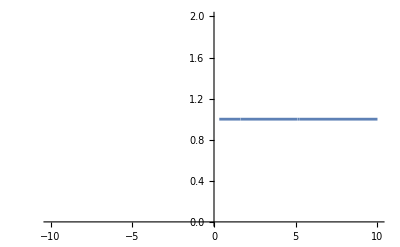

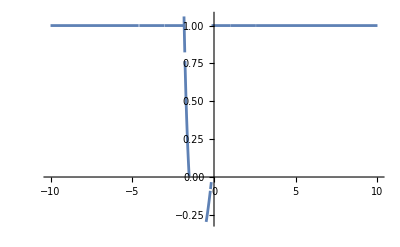

```mathematica
Plot[D[,x]/((x^3+3 x^2+9x-1)/(x^3-3 x^2-9x-13)1/(√(x^3+3x-1)))//Evaluate,{x,-10,10},WorkingPrecision->100]
Plot[D[,x]/((x^4+5 x^3+9 x^2+13x+17)/(x^4+4 x^3-6 x^2-20x-20)1/(√(x^4+4 x^3+39 x^2+70x+25)))//Evaluate,{x,-10,10},WorkingPrecision->100]
```